```mathematica
diffEq=D[ψ[x,t],t]==𝒟 D[ψ[x,t],{x,2}]
```

ψ^(0,1)[x,t]==𝒟 ψ^(2,0)[x,t]

```mathematica
bc0=ψ[0,t]==0
```

ψ[0,t]==0

```mathematica
bc1=ψ[1,t]==0
```

ψ[1,t]==0

```mathematica
ic=ψ[x,0]==Sin[π x]
```

ψ[x,0]==Sin[π x]

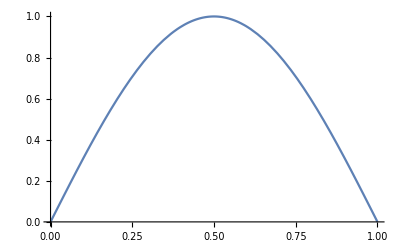

```mathematica
Plot[Sin[π x],{x,0,1}]
```

```mathematica
sol=DSolve[{diffEq,bc0,bc1,ic},ψ[x,t],{x,t}]
```

{{ψ[x,t]→ⅇ^(-π^2 t 𝒟) Sin[π x]}}

```mathematica
f[x_,t_,𝒟_]:=ⅇ^(-π^2 𝒟 t)Sin[π x]
```

```mathematica
d=1
```

1

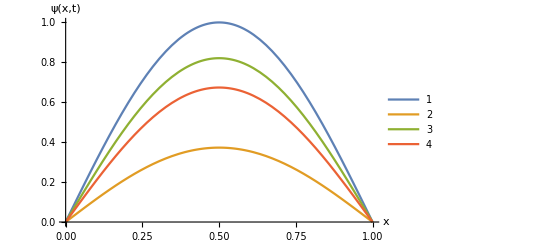

```mathematica
Plot[{f[x,0,d],f[x,0.1,d],f[x,0.02,d],f[x,0.04,d]},{x,0,1},PlotRange->Automatic,AxesLabel->{"x","ψ(x,t)"},PlotLegends->Automatic]
```